# Evaluation of e^+e^-→γγ Cross Section by The Optical Theorem

A direct consequence of unitarity of the relativsitic S-matrix is the optical theorem

2Im ℳ(s,t=0)=Flux×σ_tot,

which relates the imaginary part of the forward (t=0) elastic scattering amplitude to the total cross section.  Since the cross section itself depends on the square of the scattering amplitude

σ_Tot=1/Flux∑|ℳ(s,t)|^2(d(PS))_2,

the optical theorem provides a relationship that is nonlinear in the coupling constant—frequently the perturbation parameter.  Therefore, the optical theorem allows us to calculate cross sections at lower orders in pertubation theory using information from the higher order amplitude with the phase space integration already done.

In this tutorial, the tree level unpolarized e^+e^-→γγ cross section is obtained by calculating the imaginary part of the one loop e^+e^-→e^+e^- elastic amplitude.  In Package-X, we can limit the calculation of any one loop integral to just the discontinuity across the normal threshold cut by appropriately setting the option Part to LoopRefine:

LoopRefine[expr,Part→Discontinuity[s]] | computes the discontinuity of expr across the s-channel normal threshold cut.

Obtaining discontinuities.

Since Feynman integrals are real analytic functions of the kinematic variables, the discontinuity is proportial to the imaginary part

Disc_s(ℳ)=2i Im ℳ .

After substituting (NumberedEquation) into the optical theorem (NumberedEquation), we obtain the total cross section in terms of the discontinuity of the loop integral in the forward limit:

σ_Tot=-i/Flux Disc_s ℳ(s,t=0).

At one loop order, the Feynman diagrams are contributing to the e^+e^-→e^+e^- elastic amplitude are:

-Graphics- |

The discontinuity will be computed across the s-channel cut, indicated in red.  Both contributions will be added to obtain the correct result.

Load Package-X:

```mathematica
Needs["X`"]
```

Define set of kinematic relations for the forward scattering problem:

```mathematica
onShell={p1.p1->m^2,p2.p2->m^2,p1.p2->1/2 (-2 m^2+s)};
```

It is easiest to define the integrals in the more general kinematic configuration.  The evaluation control function Inactive is used to prevent LoopIntegrate from processing the numerator before kinematic rules for forward scattering have been applied:

```mathematica
diagram1=Inactive[LoopIntegrate][⟨𝓋[p1,m],ⅈ e Subscript[γ, μ],ⅈ(γ.k+m 𝟙),ⅈ e Subscript[γ, ν],𝓊[p2,m]⟩⟨𝓊[p4,m],ⅈ e Subscript[γ, ς],ⅈ(γ.(k+p1-p3)+m 𝟙),ⅈ e Subscript[γ, ρ],𝓋[p3,m]⟩(-ⅈ Subscript[𝕘, μ,ρ])(-ⅈ Subscript[𝕘, ν,ς]),k,{k,m},{k+p1-p3,m},{k+p1,0},{k-p2,0}]/.{p3->p1,p4->p2}
diagram2=Inactive[LoopIntegrate][⟨𝓋[p1,m],ⅈ e Subscript[γ, μ],ⅈ(γ.k+m 𝟙),ⅈ e Subscript[γ, ν],𝓊[p2,m]⟩⟨𝓊[p4,m],ⅈ e Subscript[γ, ς],ⅈ(-γ.(k-p2+p3)+m 𝟙),ⅈ e Subscript[γ, ρ],𝓋[p3,m]⟩(-ⅈ Subscript[𝕘, ν,ρ])(-ⅈ Subscript[𝕘, μ,ς]),k,{k,m},{k-p2+p3,m},{k-p2,0},{k+p1,0}]/.{p3->p1,p4->p2}
```

-e^4 ⟨𝓋[p1,m],γ_μ,ⅈ (𝟙 m+γ.k),γ_ν,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ_ς,ⅈ (𝟙 m+γ.k),γ_ρ,𝓋[p1,m]⟩ 𝕘_(μ,ρ) 𝕘_(ν,ς)kkm1km1(k+p1)01(k-p2)01

-e^4 ⟨𝓋[p1,m],γ_μ,ⅈ (𝟙 m+γ.k),γ_ν,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ_ς,ⅈ (𝟙 m-γ.k-γ.p1+γ.p2),γ_ρ,𝓋[p1,m]⟩ 𝕘_(μ,ς) 𝕘_(ν,ρ)kkm1(k+p1-p2)m1(k-p2)01(k+p1)01

Add the integrals, activate LoopIntegrate, and apply the kinematic relations.  The result is lengthy, as is usual for most next-to-leading order calculations.

```mathematica
int=Activate[diagram1+diagram2]/.onShell
```

«21»+⟨𝓋[p1,m],γ_ς,γ5,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ_ς,γ5,𝓋[p1,m]⟩ (2 m (-e^4 m PVD[0,0,0,0,4 m^2-s,m^2,s,m^2,m^2,m^2,m,m,0,0]-e^4 m PVD[0,0,0,1,4 m^2-s,m^2,s,m^2,m^2,m^2,m,m,0,0]-e^4 m PVD[0,1,0,0,4 m^2-s,m^2,s,m^2,m^2,m^2,m,m,0,0])-2 m (e^4 m PVD[0,0,0,0,4 m^2-s,m^2,s,m^2,m^2,m^2,m,m,0,0]+e^4 m PVD[0,0,1,0,4 m^2-s,m^2,s,m^2,m^2,m^2,m,m,0,0]+e^4 m PVD[0,1,0,0,4 m^2-s,m^2,s,m^2,m^2,m^2,m,m,0,0])+«7»)

At this stage we may compute the discontinuity across the s-channel normal threshold cut.

```mathematica
disc=LoopRefine[int,Part->Discontinuity[s]]
```

-1/(s √(-(4 m^2-s) s))4 e^4 m π ⟨𝓋[p1,m],γ_ρ,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],σ_(ρ,{p1}),𝓋[p1,m]⟩ HeavisideTheta[s] Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))]-1/(s √(-(4 m^2-s) s))4 e^4 m π ⟨𝓋[p1,m],γ_ς,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],σ_(ς,{p2}),𝓋[p1,m]⟩ HeavisideTheta[s] Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))]-1/(√(s (-4 m^2+s)))2 ⅈ e^4 π ⟨𝓋[p1,m],γ_ρ,γ5,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ_ρ,γ5,𝓋[p1,m]⟩ HeavisideTheta[s] Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))]+2 ⅈ π ⟨𝓋[p1,m],γ_ς,γ5,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ_ς,γ5,𝓋[p1,m]⟩ HeavisideTheta[s] (e^4/(4 m^2-s)+(2 e^4 m^2 Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) √(-(4 m^2-s) s)))+2 ⅈ π ⟨𝓋[p1,m],𝓊[p2,m]⟩⊗⟨𝓊[p2,m],𝓋[p1,m]⟩ HeavisideTheta[s] ((4 e^4 (2 m^2-s))/((4 m^2-s) s)-(16 e^4 m^4 Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))+2 ⅈ π ⟨𝓋[p1,m],γ5,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ.p1,γ5,𝓋[p1,m]⟩ HeavisideTheta[s] ((2 e^4 m)/((4 m^2-s) s)+(2 e^4 m (6 m^2-s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))+2 ⅈ π ⟨𝓋[p1,m],γ5,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ.p2,γ5,𝓋[p1,m]⟩ HeavisideTheta[s] ((2 e^4 m)/((4 m^2-s) s)+(2 e^4 m (6 m^2-s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))+2 ⅈ π ⟨𝓋[p1,m],γ_ρ,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],σ_(ρ,{p2}),𝓋[p1,m]⟩ HeavisideTheta[s] ((4 ⅈ e^4 m)/((4 m^2-s) s)-(2 ⅈ e^4 m √(-(4 m^2-s) s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 s))+2 ⅈ π ⟨𝓋[p1,m],γ_ς,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],σ_(ς,{p1}),𝓋[p1,m]⟩ HeavisideTheta[s] ((4 ⅈ e^4 m)/((4 m^2-s) s)-(2 ⅈ e^4 m √(-(4 m^2-s) s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 s))+2 ⅈ π ⟨𝓋[p1,m],σ_(ρ,ς),𝓊[p2,m]⟩⊗⟨𝓊[p2,m],σ_(ρ,ς),𝓋[p1,m]⟩ HeavisideTheta[s] (-e^4/(4 m^2-s)+(2 e^4 m^2 √(-(4 m^2-s) s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 s))+2 ⅈ π ⟨𝓋[p1,m],𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ.p1,𝓋[p1,m]⟩ HeavisideTheta[s] (-(18 e^4 m)/((4 m^2-s)^2)-(6 e^4 m (2 m^2+s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 √(-(4 m^2-s) s)))+2 ⅈ π ⟨𝓋[p1,m],𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ.p2,𝓋[p1,m]⟩ HeavisideTheta[s] ((18 e^4 m)/((4 m^2-s)^2)+(6 e^4 m (2 m^2+s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 √(-(4 m^2-s) s)))+2 ⅈ π ⟨𝓋[p1,m],γ_ρ,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],γ_ρ,𝓋[p1,m]⟩ HeavisideTheta[s] ((e^4 (8 m^2-5 s))/((4 m^2-s) s)-(e^4 (16 m^4-10 m^2 s+3 s^2) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))

This expression may be directly interpreted as arising from the squaring the tree-level e^+e^-→γγ amplitude, and summing over final state degrees of freedom (photon helicities and momenta).  The various spinors v̄(p_1)...u(p_2)ū(p_2)...v(p_2) are associated with the initial-state electron and positron.  To obtain the spin-averaged cross section, apply the completeness relations:

∑u(p_2)ū(p_2)=(p/)_2+m
∑v(p_1)v̄(p_1)=(p/)_1-m

to convert the spinor products into traces:

∑v̄(p_1)...u(p_2)ū(p_2)...v(p_2)=Tr[((p/)_1-m)...((p/)_2+m)...] .

Replace all FermionLineProduct objects with the appropriate trace (Spur), and divide by 4 to account for averaging:

```mathematica
1/4 disc/.⟨𝓋[p1,m],mtx1___,𝓊[p2,m]⟩⊗⟨𝓊[p2,m],mtx2___,𝓋[p1,m]⟩:>Contract[Spur[p1.γ-m 𝟙,mtx1,p2.γ+m 𝟙,mtx2]]
```

1/4 (-(2 ⅈ e^4 π HeavisideTheta[s] (4 𝒹 m^2+8 p1.p2-4 𝒹 p1.p2) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/(√(s (-4 m^2+s)))-1/(s √(-(4 m^2-s) s))4 e^4 m π HeavisideTheta[s] (-4 ⅈ m p1.p1+4 ⅈ 𝒹 m p1.p1-4 ⅈ m p1.p2+4 ⅈ 𝒹 m p1.p2) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))]-1/(s √(-(4 m^2-s) s))4 e^4 m π HeavisideTheta[s] (-4 ⅈ m p1.p2+4 ⅈ 𝒹 m p1.p2-4 ⅈ m p2.p2+4 ⅈ 𝒹 m p2.p2) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))]+2 ⅈ π HeavisideTheta[s] (4 𝒹 m^2+8 p1.p2-4 𝒹 p1.p2) (e^4/(4 m^2-s)+(2 e^4 m^2 Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) √(-(4 m^2-s) s)))+2 ⅈ π HeavisideTheta[s] (-4 m^2+4 p1.p2) ((4 e^4 (2 m^2-s))/((4 m^2-s) s)-(16 e^4 m^4 Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))+2 ⅈ π HeavisideTheta[s] (-4 m p1.p1-4 m p1.p2) ((2 e^4 m)/((4 m^2-s) s)+(2 e^4 m (6 m^2-s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))+2 ⅈ π HeavisideTheta[s] (-4 m p1.p2-4 m p2.p2) ((2 e^4 m)/((4 m^2-s) s)+(2 e^4 m (6 m^2-s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s)))+2 ⅈ π HeavisideTheta[s] (-4 ⅈ m p1.p1+4 ⅈ 𝒹 m p1.p1-4 ⅈ m p1.p2+4 ⅈ 𝒹 m p1.p2) ((4 ⅈ e^4 m)/((4 m^2-s) s)-(2 ⅈ e^4 m √(-(4 m^2-s) s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 s))+2 ⅈ π HeavisideTheta[s] (-4 ⅈ m p1.p2+4 ⅈ 𝒹 m p1.p2-4 ⅈ m p2.p2+4 ⅈ 𝒹 m p2.p2) ((4 ⅈ e^4 m)/((4 m^2-s) s)-(2 ⅈ e^4 m √(-(4 m^2-s) s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 s))+2 ⅈ π HeavisideTheta[s] (4 𝒹 m^2-4 𝒹^2 m^2+16 p1.p2-20 𝒹 p1.p2+4 𝒹^2 p1.p2) (-e^4/(4 m^2-s)+(2 e^4 m^2 √(-(4 m^2-s) s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 s))+2 ⅈ π HeavisideTheta[s] (4 m p1.p1-4 m p1.p2) (-(18 e^4 m)/((4 m^2-s)^2)-(6 e^4 m (2 m^2+s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 √(-(4 m^2-s) s)))+2 ⅈ π HeavisideTheta[s] (4 m p1.p2-4 m p2.p2) ((18 e^4 m)/((4 m^2-s)^2)+(6 e^4 m (2 m^2+s) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s)^2 √(-(4 m^2-s) s)))+2 ⅈ π HeavisideTheta[s] (-4 𝒹 m^2+8 p1.p2-4 𝒹 p1.p2) ((e^4 (8 m^2-5 s))/((4 m^2-s) s)-(e^4 (16 m^4-10 m^2 s+3 s^2) Log[(-s^2+s √(s (-4 m^2+s)))/(-s^2-s √(s (-4 m^2+s)))])/((4 m^2-s) s √(-(4 m^2-s) s))))

Apply the kinematic relations, take 𝒹→4, and simplify the expression (the normalization factor 1/16 π^2 has been restored):

```mathematica
discAv=1/(16 π^2)Simplify[%/.onShell/.𝒹->4]
```

-1/(4 π s √(s (-4 m^2+s)))ⅈ e^4 HeavisideTheta[s] (√(s (-4 m^2+s)) (4 m^2+s)+(-8 m^4+4 m^2 s+s^2) Log[(s-√(s (-4 m^2+s)))/(s+√(s (-4 m^2+s)))])

To convert this into a cross section, multiply by -i/Flux as indicated in (NumberedEquation).  By expressing the result in terms of the velocity: s=4m^2/(1-β^2), the total cross section can be brought to a recognizable form.

```mathematica
flux=2 √Kallenλ[s,m^2,m^2];
```

```mathematica
crossXn=Simplify[-ⅈ/flux discAv/.{s->(4 m^2)/(1-β^2)},Assumptions->β>0&&β<1&&m>0]/.e->√(4π α)
```

-(π α^2 (-1+β^2) (2 β (-2+β^2)+(-3+β^4) Log[(1-β)/(1+β)]))/(4 m^2 β^2)

Observe that the normalization factor correctly reflects the indistinguishability of the final state photons.

Make a plot:

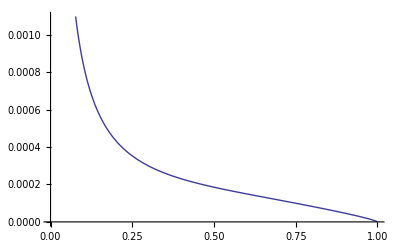

```mathematica
Plot[Evaluate[crossXn/.{α->1/137,m->1}],{β,0,1}]
```

More About

Package-X